-1/(-1184000+r)^2

2/(-1184000+r)^3

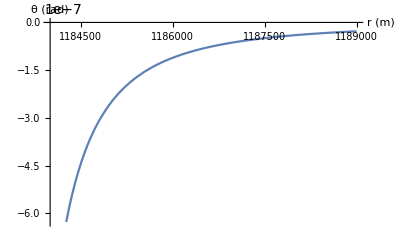

1/Abs[1+2/(-1184000+r)^3]

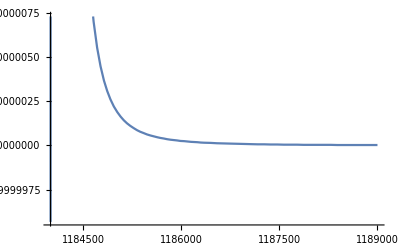

{1184000,1184001,1184002,1184003,1184004,1184005,1184006,1184007,1184008,1184009,1184010,1184011,1184012,1184013,1184014,1184015,1184016,1184017,1184018,1184019,1184020,1184021,1184022,1184023,1184024,1184025,1184026,1184027,1184028,1184029,1184030,1184031,1184032,1184033,1184034,1184035,1184036,1184037,1184038,1184039,1184040,1184041,1184042,1184043,1184044,1184045,1184046,1184047,1184048,1184049,1184050}

Power::infy: Infinite expression 1/0 encountered.

{0,1,4/3,27/25,32/31,125/123,108/107,343/341,256/255,729/727,500/499,1331/1329,864/863,2197/2195,1372/1371,3375/3373,2048/2047,4913/4911,2916/2915,6859/6857,4000/3999,9261/9259,5324/5323,12167/12165,6912/6911,15625/15623,8788/8787,19683/19681,10976/10975,24389/24387,13500/13499,29791/29789,16384/16383,35937/35935,19652/19651,42875/42873,23328/23327,50653/50651,27436/27435,59319/59317,32000/31999,68921/68919,37044/37043,79507/79505,42592/42591,91125/91123,48668/48667,103823/103821,55296/55295,117649/117647,62500/62499}

```mathematica
Clear["Global`*"];


(* get list of refractive angles and refractive angle derivatives from some atmosphere shell parameters *)

(* calculate derivatives of refractivies from eqs 2 and 3 in C&E *)
	(* just making up some θ and dθ function here... *)
rPluto = 1184000; (* m *)
dPluto = 4.864*10^15;  (*cm; distance from Earth to Pluto (1989 value from Elliot et al paper) *)

θ=-1/(r-rPluto)^2
dθ=D[θ,r]

θFunc[r_] := -1/(r-rPluto)^2;
dθFunc[r_] := -2/(r-rPluto)^3;
Plot[θFunc[r+1000],{r,rPluto,rPluto+5000},AxesLabel->{"r (m)","θ (rad)"}]

(* get radius as a function of time using eq 5 (and some other transformations) *)


(* use eq 1 to get flux as a function of radius (and thus, flux as a function of time) to generate light curve *)
ϕ=1/Abs[1+D[dθ]]
ϕFunc[r_]:=1/Abs[1+D[-2/(r-rPluto)^3]];
Plot[ϕFunc[r],{r,rPluto,rPluto+5000}]

sample = Range[rPluto,rPluto+50,1]
ϕFunc[sample]
```